```mathematica
SetDirectory[NotebookDirectory[]];
Get["eigenfaces-algorithm.m"]
```

```mathematica
makeGrid[trainingData_,testData_,numEF_]:=Module[{},
neutralFaces=trainingData[[All,1]];
normalizedFaces=Map[#-Mean[#]&, Flatten/@trainingData[[All,1]]];
{eigenvalues, eigenfaces}=findEigenfaces[normalizedFaces];
trainingFaces=Map[eigenCompress[#,eigenfaces,numEF]&,normalizedFaces];
Grid@Table[Join[{Image[face[[1]]],"→"},matches=recognizeFace[face[[1]],numEF,1][[1]];trainingData[[matches,2]]],{face,testData}]
]
```

```mathematica
FOM[trainingData_,testData_,numEF_]:=Module[{},
neutralFaces=trainingData[[All,1]];
normalizedFaces=Map[#-Mean[#]&, Flatten/@trainingData[[All,1]]];
{eigenvalues, eigenfaces}=findEigenfaces[normalizedFaces];
trainingFaces=Map[eigenCompress[#,eigenfaces,numEF]&,normalizedFaces];
(*Grid@Table[Join[{Image[face[[1]]],"→"},matches=recognizeFace[face[[1]],numEF,1][[1]];trainingData[[matches,2]]],{face,testData}];*)
matchesFound=Table[{face[[2]],trainingData[[recognizeFace[face[[1]],numEF,1][[1,1]]]][[2]]},{face,testData}];
successpercent=(Length@Cases[matchesFound,{x_,x_}])/(Length@matchesFound)
]
```

```mathematica
trainingFaces[[1;;5]]
```

{{-50.9498},{-67.575},{0.516874},{-34.4243},{-57.7749}}

# Neutral faces training

```mathematica
labelledFaces=MapThread[Labeled[#1,#2]&,{images,Catenate@Transpose@ConstantArray[names,8]}];
```

## Train on 43, test on 301 (sampled)

```mathematica
ImageDimensions[CurrentImage[]]
```

{320,240}

```mathematica
Dimensions@eric
```

{360,256}

```mathematica
Dynamic[camface=ColorConvert[ImageCrop[ImageReflect[CurrentImage[RasterSize->{640,480}],Left],{256,360}],"Grayscale"]
]
```

```mathematica
Dynamic@recognizeFace[ImageData@camface,All,1]
```

```mathematica
N@FOM[labelledFaces[[1;;All;;8]],labelledFaces[[6;;All;;8]],2]
```

39.5349 %

```mathematica
data=Table[FOM[labelledFaces[[1;;All;;8]],labelledFaces[[s;;All;;8]],d],{s,2,8},{d,1,43}];
Dimensions@data
```

{7,43}

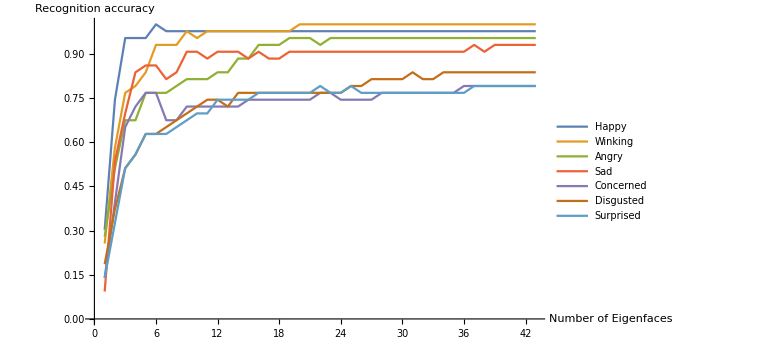

```mathematica
ListLinePlot[data,PlotRange->{{0,All},{0,1}},PlotLegends->emotions[[2;;8]],ImageSize->Large,AxesLabel->{"Number of Eigenfaces","Recognition accuracy"}]
```

```mathematica
Length@labelledFaces/8
```

43

```mathematica
makeGrid[labelledFaces[[1;;All;;8]],labelledFaces[[7;;All;;8]],All]
```

-Graphics- | → | Ariana
-Graphics- | → | Jonah
-Graphics- | → | Charlie
-Graphics- | → | Chloe
-Graphics- | → | Ariana
-Graphics- | → | Jonah
-Graphics- | → | David
-Graphics- | → | Eric
-Graphics- | → | Diego
-Graphics- | → | Emily
-Graphics- | → | Eric
-Graphics- | → | Gwen
-Graphics- | → | Harper
-Graphics- | → | Isaac
-Graphics- | → | Izzy
-Graphics- | → | John
-Graphics- | → | John
-Graphics- | → | John
-Graphics- | → | Chris
-Graphics- | → | Kaitlyn
-Graphics- | → | Kevin
-Graphics- | → | Lauren
-Graphics- | → | Joseph
-Graphics- | → | Lydia
-Graphics- | → | Margo
-Graphics- | → | Mark
-Graphics- | → | Mary
-Graphics- | → | Max
-Graphics- | → | Mica
-Graphics- | → | Nathan
-Graphics- | → | Paige
-Graphics- | → | Rebecca
-Graphics- | → | Regina
-Graphics- | → | Ruby
-Graphics- | → | Sam
-Graphics- | → | Sarah
-Graphics- | → | Sean
-Graphics- | → | Siddhartan
-Graphics- | → | Min
-Graphics- | → | Sung
-Graphics- | → | Kaitlyn
-Graphics- | → | Uma
-Graphics- | → | Willem

```mathematica
f[x_]:=x+5
```

```mathematica
f[7]
```

12

```mathematica
f[6]="hello"
```

hello